# Fig. 4 of Bull, Wichman, Krone

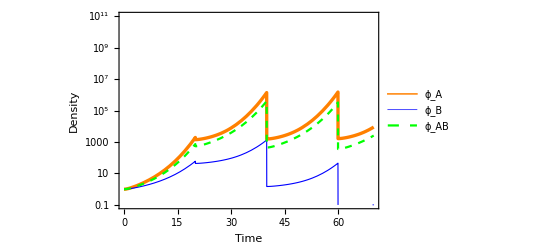

```mathematica
Pars={r->0.1,
 Subscript[b, AA]-> 20,Subscript[b, BB]-> 10,Subscript[b, GA]-> 17,Subscript[b, GB]-> 17, Subscript[b, AB]-> .01,Subscript[b, BA]-> .01,
Subscript[k, AA]->.000000001,Subscript[k, BB]->.000000001,Subscript[k, BA]-> 0.0, Subscript[k, AB]-> 0.0,
Subscript[k, GA]->.000000001,Subscript[k, GB]->.000000001, λ-> 1};

Sols=NDSolve[
{
Subscript[C, A]'[t]==(Subscript[C, A][t](r - Subscript[k, AA] Subscript[P, AA][t] - Subscript[k, BA] Subscript[P, BA][t]- Subscript[k, GA] Subscript[P, GA][t])/.Pars), 
Subscript[C, B]'[t]==(Subscript[C, B][t](r - Subscript[k, BB] Subscript[P, BB][t] - Subscript[k, AB] Subscript[P, AB][t]- Subscript[k, GB] Subscript[P, GB][t])/.Pars),

Subscript[P, AA]'[t]==(Subscript[b, AA] λ Subscript[In, AA][t]  - Subscript[k, AA] Subscript[P, AA][t] Subscript[C, A][t])/.Pars,
Subscript[In, AA]'[t]==(Subscript[k, AA] Subscript[P, AA][t] Subscript[C, A][t]  - λ Subscript[In, AA][t])/.Pars,     (* Infected state*)

Subscript[P, AB]'[t]==0.0/.Pars,  (* Phage A just sits in culture of B*)

Subscript[P, BB]'[t]==(Subscript[b, BB] λ Subscript[In, BB][t]  - Subscript[k, BB] Subscript[P, BB][t] Subscript[C, B][t])/.Pars,
Subscript[In, BB]'[t]==(Subscript[k, BB] Subscript[P, BB][t] Subscript[C, B][t]  - λ Subscript[In, BB][t])/.Pars,

Subscript[P, BA]'[t]==0.0/.Pars,   (* Phage B just sits in culture of A*)

Subscript[P, GA]'[t]==(Subscript[b, GA] λ Subscript[In, GA][t]  - Subscript[k, GA] Subscript[P, GA][t] Subscript[C, A][t])/.Pars,
Subscript[In, GA]'[t]==(Subscript[k, GA] Subscript[P, GA][t] Subscript[C, A][t]  - λ Subscript[In, GA][t])/.Pars,

Subscript[P, GB]'[t]==(Subscript[b, GB] λ Subscript[In, GB][t]  - Subscript[k, GB] Subscript[P, GB][t] Subscript[C, B][t])/.Pars,
Subscript[In, GB]'[t]==(Subscript[k, GB] Subscript[P, GB][t] Subscript[C, B][t]  - λ Subscript[In, GB][t])/.Pars,

S'[t] == 0.0/.Pars,


Subscript[C, A][0]==1*^7,Subscript[C, B][0]==1*^7,
Subscript[P, AA][0]== 1,Subscript[P, AB][0] == 0,Subscript[P, BB][0] == 1,Subscript[P, BA][0] == 0, 
Subscript[In, AA][0]== 0,
Subscript[In, BB][0] == 0,
Subscript[P, GA][0]==.5,Subscript[P, GB][0]==.5,
Subscript[In, GA][0]==0,Subscript[In, GB][0]==0,

S[0]==0.0,

WhenEvent[Mod[t,20]≤.0001  && t>9,
{   (*Should set everything summing to 1000 for next cycle*)
Subscript[C, A][t]->1*^7,Subscript[C, B][t]->1*^7,

Subscript[In, AA][t]-> 0.0,   (* Set all infections to 0*)
Subscript[In, BB][t] -> 0.0,
Subscript[In, GA][t]-> 0.0,
Subscript[In, GB][t] -> 0.0,

(*Sum all densities; include infections as backup; only 4 should be >0 *)
S[t]-> (
Subscript[P, AA][t]+Subscript[P, AB][t] +Subscript[In, AA][t]+
Subscript[P, BB][t] +Subscript[P, BA][t] + Subscript[In, BB][t] +
Subscript[P, GA][t]+Subscript[In, GA][t]+
Subscript[P, GB][t]+Subscript[In, GB][t]
),

Subscript[P, AA][t]->  1000*(Subscript[P, AA][t]+Subscript[P, AB][t] )/(S[t]), 
Subscript[P, AB][t] -> Subscript[P, AA][t],

Subscript[P, BB][t]->  1000*(Subscript[P, BB][t]+Subscript[P, BA][t] )/(S[t]), 
Subscript[P, BA][t] -> Subscript[P, BB][t],

Subscript[P, GA][t]->  1000*(Subscript[P, GA][t]+Subscript[P, GB][t])/(S[t]),
Subscript[P, GB][t]->  Subscript[P, GA][t]
}]
},

{Subscript[C, A],Subscript[C, B],Subscript[P, AA],Subscript[In, AA],Subscript[P, AB],Subscript[P, BB],Subscript[In, BB],Subscript[P, BA],Subscript[P, GA],Subscript[P, GB],Subscript[In, GA],Subscript[In, GB], S},{t,.001,700}   ];

plot = LogPlot[
{
Evaluate [(Subscript[P, AA][t]+Subscript[P, AB][t] +Subscript[In, AA][t])/.Sols],
Evaluate [(Subscript[P, BB][t] +Subscript[P, BA][t] + Subscript[In, BB][t] )/.Sols],
Evaluate [(Subscript[P, GA][t]+Subscript[In, GA][t]+Subscript[P, GB][t]+Subscript[In, GB][t])/.Sols]},
{t,0,70},
PlotRange->{1*^-1,1*^11},Frame->True, 
FrameLabel->{"Time","Density"},
PlotStyle->{(*Directive[Black,Dashed], Directive[Thickness[.001],Black],*)Directive[Thickness[0.006],Orange],Directive[Thickness[0.002],Blue],Directive[Green,Dashed]},
PlotLegends->{(*"B_A",Subscript[B, B],*)"ϕ_A","ϕ_B","ϕ_AB"},
BaseStyle->{FontSize -> 16},LabelStyle->Directive[Blue,16]]
```